```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/youngsam/Code/SULI/GitHub/grb/2D_correlation/151027A

## GOOD FITTINGS

```mathematica
Kann[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};
(*NegativeDetected=0*)
Do[
If[Head[c[[i,1]]]==Real,{

time=c[[i,1]];
beta=c⟦i,5⟧;
z=c⟦i,6⟧;

If[time>0,
logtime=Log[10,time];
flux=c⟦i,2⟧;
fluxposerr=c⟦i,3⟧;
fluxnegerr=c⟦i,4⟧;

(*flux version*)
(*taking logs for flux*)
logflux=Log[10,c⟦i,2⟧];
logfluxerror=((c⟦i,3⟧+c⟦i,4⟧)/2)/(c[[i,2]]*Log[10]);
(*how to account for pos and neg error?*)
(*check if 1si or 2sig; 1sig = divide by 2, 2sig = divide by 2*1.65*)

If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
]
,{i,1,Length[c]}];
)
```

```mathematica
Wczytywanie[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};
(*NegativeDetected=0*)
Do[
If[Head[c[[i,1]]]==Real,{

beta=c⟦i,5⟧;
z=c⟦i,6⟧;
time=c[[i,1]]*(1+z);

If[time>0,
logtime=Log[10,time]; (*multiply by 1+z to get from rest to obs frame*)
flux=c⟦i,2⟧*((1+z)^(1-beta)); (*multiply by k-corr to get from rest->obs frame*)
fluxposerr=c⟦i,3⟧*((1+z)^(1-beta));
fluxnegerr=c⟦i,4⟧*((1+z)^(1-beta));

logflux=Log[10,flux];
logfluxerror=((fluxposerr+fluxnegerr)/2)/(flux*Log[10]);
If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
]
,{i,1,Length[c]}];
)
```

```mathematica
(* use si if 3 columns *)
Si[a_]:=(
c={};
b=Import[a,"Table"]; (*confirmed: importing entire file*)
For[i=1,b[[i,2]]!="photon",i++,];
c=Take[b,i-1];
table={};
dane={}; (*dane = data*)
Δt={};
ΔF={};

Do[
If[Head[c[[i,1]]]==Real,{
time=c[[i,1]];
If[time>0,
logtime=Log[10,time];
flux=c⟦i,2⟧;
logflux=Log[10,c⟦i,2⟧];
band=c⟦i, 4⟧;

logfluxerror=c⟦i,3⟧/(c[[i,2]]*Log[10]);(*check if 1si or 2sig; 1sig = divide by 2, 2sig = divide by 2*1.65*)


If[flux>0,AppendTo[table,{logtime,logflux,logfluxerror,band}]];
If[flux>0,AppendTo[dane,{logtime,logflux}]];
(*If[flux>0,AppendTo[Δt,logerrorontime]];*)
If[flux>0,AppendTo[ΔF,logfluxerror]];
]}
] 
,{i,1,Length[c]}];
)
```

```mathematica
Dzielenie[start_,end_]:= (*beginning of plateau emission, where you start and end the curve-fitting*)
(
Clear[counter];
startp=start ;
endp=end;
Part1={};
Δt1={};
ΔF1={};
Part2={};
Δt2={};
ΔF2={};
counter=0;

Do[If[startp≤dane[[i,1]]≤endp,
(
AppendTo[Part1,dane[[i]]];
AppendTo[Δt1,Δt[[i]]];
AppendTo[ΔF1,ΔF[[i]]];
counter=counter+1;
),
(
AppendTo[Part2,dane[[i]]];
AppendTo[Δt2,Δt[[i]]];
AppendTo[ΔF2,ΔF[[i]]];
)
],{i,1,Length[dane]}];

Print["number of points included: ",counter]
);
```

```mathematica
model[F_,T_,α_,t_]:=Piecewise[{{Log[10,10^F*Exp[α-(10^x*α/10^T)]*Exp[-Abs[t]/10^x]],10^x<10^T},{Log[10,10^F*(10^x/10^T)^(-α)*Exp[-Abs[t]/10^x]],10^x≥10^T}}];
```

```mathematica
(* a = F, b = T, c = alpha, d = t *)

fitowanie[a_,b_,c_,d_,er_,datapart_,beg_,end_]:=
(fit1=NonlinearModelFit[datapart,model[F,T,α,t],{{F,a},{T,b},{α,c},{t,d}},x,Weights->1/er^2];
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
Print["----------------------------------------------"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidence intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];


(*if Subscript[t, a] is <0 we have to fix it and refit in order for following Δχ^2 calculations*)
If[fit1["BestFitParameters"][[4,2]]≤0,
(
Clear[bestparameters];
startowe={{F,a},{T,b},{α,c}};
fit1=NonlinearModelFit[datapart,model[F,T,α,0],startowe,x,Weights->1/er^2]; (*this line has t=0*)
bestparameters=fit1["BestFitParameters"];
besterrors=fit1["ParameterErrors"];
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]],t->0};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]}}&[bestparameters];
Flux=model[F,T,α,0]/.bestparameters;
Print["!!!!!!!!!!!!!!!!!!! changing best fit parameters to: ",bestparameters," with fixed ta->0"];
Print["best fit parameters: ",bestparameters];
Print["theirs errors: ",besterrors];
Print["confidency intervals: ",fit1["ParameterConfidenceIntervals",ConfidenceLevel->0.68]];
),
(
zamiana[i_,k_]:={parametr[[i]]->FaTaTable[[i,k]]};
start={{F,#[[1,2]]},{T,#[[2,2]]},{α,#[[3,2]]},{t,#[[4,2]]}}&[bestparameters];
Flux=model[F,T,α,t]/.bestparameters
)
];
Print[
Show[
Plot[model[F,T,α,t]/.bestparameters/.t->0,{x,beg,end}],ListPlot[datapart,PlotRange->All],ListPlot[{{bestparameters[[2]][[2]],bestparameters[[1]][[2]]}},PlotStyle->{Green, PointSize[0.05]},PlotRange->All],
PlotRange->All,FrameLabel->{"log time rest frame (s)","log Flux (erg s^-1)"}]]
Print["----------------------------------------------"];
Clear[fit1];
)
```

```mathematica
Wycinanie[a_,b_]:=
(
przedziałT:=Interval[{a[[1]],b[[1]]}]; (*compartments = bins?*)
przedziałF:=Interval[{a[[2]],b[[2]]}];
Do[
If[!IntervalMemberQ[przedziałT,dane[[i,1]]]||!IntervalMemberQ[przedziałF,dane[[i,2]]],
(
AppendTo[Part12,dane[[i]]];
AppendTo[Δt12,Δt[[i]]];
AppendTo[ΔF12,ΔF[[i]]];
)
];
,{i,1,Length[dane]}];

dane=Part12;
Δt=Δt12;
ΔF=ΔF12;

Part12={};
Δt12={};
ΔF12={};
)
```

```mathematica
Chisquare[datapart_,er_]:=Module[{ν,REDUCED},


singleχ[j_]:=(1/er[[All]](datapart[[All,2]]-Flux/.x->datapart[[All,1]]))^2;

bestfitχ=Sum[singleχ[All],{All,1,Length[datapart]}];
REDUCED=bestfitχ/(Length[datapart]-3);
ν=Length[datapart];
X=REDUCED ν;
PROBABILITY=2^(-ν/2)/Gamma[ν/2] NIntegrate[ⅇ^(-x/2) x^(-1+ν/2),{x,X,Infinity}];
Print["GRB ",id," afterglow has"," χ^2: ",bestfitχ," and  reduced χ^2: ",REDUCED," α: ",Chop[PROBABILITY]];
];
```

```mathematica
IntervalEstimating[b_,e_,s_,datapart_,er_]:=
(
Print["--------------testing-------------"];
FaTaTable={};

parametr=Table[bestparameters[[i,1]],{i,1,3}];
bestparam=Table[bestparameters[[i,2]],{i,1,3}];
errors=Table[besterrors[[i]],{i,1,3}];

beg=b;                                             (*flexible interval for error multiplier*)
end=e;
step=s;
multiplier=Sort[Join[Table[-end+i step,{i,0,(end-beg)/step}],Table[beg+i step,{i,0,(end-beg)/step}]]];
Do[
values=Table[bestparam[[j]]+multiplier[[i]]*errors[[j]],{i,1,Length[multiplier]}];
AppendTo[FaTaTable,values]
,{j,1,3}];

quantity=2 ((end-beg)/step+1);

Print["---------------------------------"];

(*******  main ugly loop for Δχ^2 calculations :) ********)
Clear[Flux1];
singleχ[j_]:=((datapart[[j,2]]-Flux1/.x->datapart[[j,1]])/er[[j]])^2;
Δtable={{},{},{},{}};
finaltable={};
Print["---------------------------------"];
Do[

Do[
parametry=Drop[start,{i}];

fit12=NonlinearModelFit[datapart,model[F,T,α,t]/.zamiana[i,k],parametry,x,Weights->1/er^2];

Clear[χsquare,Flux1];
Flux1=model[F,T,α,t]/.fit12["BestFitParameters"]/.zamiana[i,k];
χsquare=Sum[singleχ[j],{j,1,Length[datapart]}];
Δχ=χsquare-bestfitχ;

AppendTo[Δtable[[i]],{multiplier[[k]],Chop[Δχ]}];

(*Print[Row[{"σ x ",multiplier[[k]],"   ","Δχ:",Chop[Δχ],"   ",zamiana[i,k],"  ",χsquare," ",fit12["BestFitParameters"]}]] ;*)
(*checking tool{set "i" for one value}*)
,{k,1,quantity}];


Clear[left,right,leftm,rightm];
left=Drop[Δtable[[i]],(-Length[Δtable[[i]]])/2];
right=Drop[Δtable[[i]],Length[Δtable[[i]]]/2];

Do[
(*Print[left[[t,2]],">3.5>",left[[t+1,2]]," ",left[[t,2]]≥3.5≥left[[t+1,2]]];*)
If[left[[t,2]]≥1≥left[[t+1,2]],leftm=((left[[t+1,1]]-left[[t,1]])(1-left[[t,2]]))/(left[[t+1,2]]-left[[t,2]])-left[[t,1]]];
If[right[[t,2]]≤1≤right[[t+1,2]],rightm=((right[[t+1,1]]-right[[t,1]])(1-right[[t,2]]))/(right[[t+1,2]]-right[[t,2]])-right[[t,1]]];
,{t,1,Length[Δtable[[i]]]/2-1}];
Print[leftm," ",rightm];
AppendTo[finaltable,
{bestparameters[[i,1]],
bestparameters[[i,2]],
(Sort[{If[NumericQ[leftm],bestparameters[[i,2]]+leftm besterrors[[i]],"error"],If[NumericQ[rightm],bestparameters[[i,2]]+rightm besterrors[[i]],"error"]}])}];

Clear[leftm,rightm];
,{i,1,3}];
(*parameters*)

Print[
TableForm[
Table[{finaltable[[i,1]],finaltable[[i,2]],"("<>ToString[finaltable[[i,3,1]]]<>" ,",ToString[finaltable[[i,3,2]]]<>")"},{i,1,3}]
,TableHeadings->{None,{"parameter","best fit"," confidency","interval"}}]];

Print[Row[Table[ListPlot[Δtable[[i]],PlotRange->All,ImageSize->Medium,PlotLabel->ToString[parametr[[i]]],FrameLabel->{"σ multiplier","Δχ^2"},Axes->False,Frame->True]
,{i,1,3}]]];

Print["---------------------------------"];
);
```

```mathematica
n = 0.05;
```

Part::partw: Part 60 of {{24.,5.64105×10^-11,1.04522×10^-11,R,nissim},{79.2,4.77962×10^-11,8.8536×10^-12,R,nissim},{126.,6.5371×10^-11,1.2112×10^-11,R,nissim},«6»,{1556.,2.65099×10^-11,4.91047×10^-12,R,nissim},«49»} does not exist.

Part::partw: Part 2 of {{78622.,1.20085×10^-12,5.77052×10^-14,I,manual}} does not exist.

Part::partw: Part 2 of {{20160.,8.65243×10^-12,3.98631×10^-13,Rc,manual}} does not exist.

Part::partw: Part 3 of {{166550.,2.67363×10^-13,9.85801×10^-15,r,manual},{252244.,1.22209×10^-13,9.00648×10^-15,r,manual}} does not exist.

Part::partw: Part 2 of {{307.,9.30083×10^-11,4.28342×10^-12,u,manual}} does not exist.

Part::partw: Part 2 of {{49488.,2.10689×10^-12,4.85603×10^-13,v,manual}} does not exist.

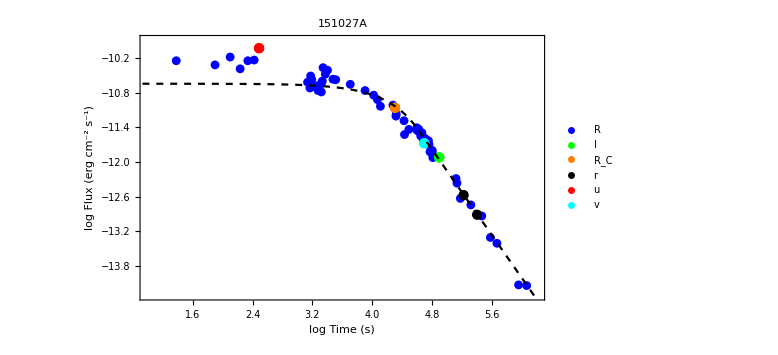

```mathematica
Si["R.txt"](*Check again*)
Rplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",Black,18},PlotStyle->Blue,RotateLabel->True,FrameLabel->{"log Time (s)","log Flux (erg cm^-2 s^-1)"},Frame->True,FrameStyle->Directive[Thick,20,Black],ImageSize->Large,PlotLegends->Placed[{"R"},{0.859+0.07,0.92}],PlotLabel-> "151027A"];
Si["I.txt"](*Check again*)
Iplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",16},PlotStyle->Green,RotateLabel->True,FrameLabel->{"Log Time (s)","Log Flux (erg/s)"},Frame->True,FrameStyle->Directive[Thin,Black],ImageSize->Large,PlotLegends->Placed[{"I"},{0.85+0.07,0.86}]];
Si["R_c.txt"](*Check again*)
Rcplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",16},PlotStyle->Orange,RotateLabel->True,FrameLabel->{"Log Time (s)","Log Flux (erg/s)"},Frame->True,FrameStyle->Directive[Thin,Black],ImageSize->Large,PlotLegends->Placed[{"R_C"},{0.866+0.07,0.80}]];
Si["littler.txt"](*Check again*)
littlerplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",16},PlotStyle->Black,RotateLabel->True,FrameLabel->{"Log Time (s)","Log Flux (erg/s)"},Frame->True,FrameStyle->Directive[Thin,Black],ImageSize->Large,PlotLegends->Placed[{"r"},{0.853+0.07,0.74}]];
Si["u.txt"](*Check again*)
uplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",16},PlotStyle->Red,RotateLabel->True,FrameLabel->{"Log Time (s)","Log Flux (erg/s)"},Frame->True,FrameStyle->Directive[Thin,Black],ImageSize->Large,PlotLegends->Placed[{"u"},{0.853+0.07,0.68}]];
Si["V.txt"](*Check again*)
vplot=ListPlot[dane,PlotRange->{{1,6.2},{-14.3,-9.9}},Frame->True,Axes->False,LabelStyle->{"Symbol",16},PlotStyle->Cyan,RotateLabel->True,FrameLabel->{"Log Time (s)","Log Flux (erg/s)"},Frame->True,FrameStyle->Directive[Thin,Black],ImageSize->Large,PlotLegends->Placed[{"v"},{0.852+0.07,0.62}]];

fit = fit =Plot[model[-11.45078032,4.619188487,1.852192054,0],{x,0,7}, PlotStyle->{Black, Dashed}];

Show[Rplot,Iplot, Rcplot, littlerplot,uplot,vplot, fit]
```